```mathematica
l = {0.45, 0.2, 0.1, 0.25, 0.15}
op = {2*10^8, 7*10^8, 9 * 10^8, 5*10^8, 9*10^8}
maxV = {0.004437, 0.005376, 0.002048, 0.005461, 0.00512}
```

{0.45,0.2,0.1,0.25,0.15}

{200000000,700000000,900000000,500000000,900000000}

{0.004437,0.005376,0.002048,0.005461,0.00512}

```mathematica
getQ[oper_, cpuSpeed_] := oper/cpuSpeed
getV[maxV_, l_] := maxV * l
getP[l_, q_] := l * q
getU[w_, q_] := w + Total[q]
getR[p_, k_] := Total [Table[p[[i]], {i, 1, k}]]
getW[cpu_, op_, l_, maxV_, v_] := Total[l * getQ[op, cpu]^2]*(1 + v^2)/(2(1-Total[getP[getV[maxV, l], getQ[op, cpu]]]))
getW[cpu_, op_, l_, maxV_, v_, k_] := Total[(l * getQ[op, cpu]^2) * (1 + v^2)]/(2 * (1 - getR[getP[l, getQ[op, cpu]], k]) * (1 - getR[getP[l, getQ[op, cpu]], k - 1]) )
```

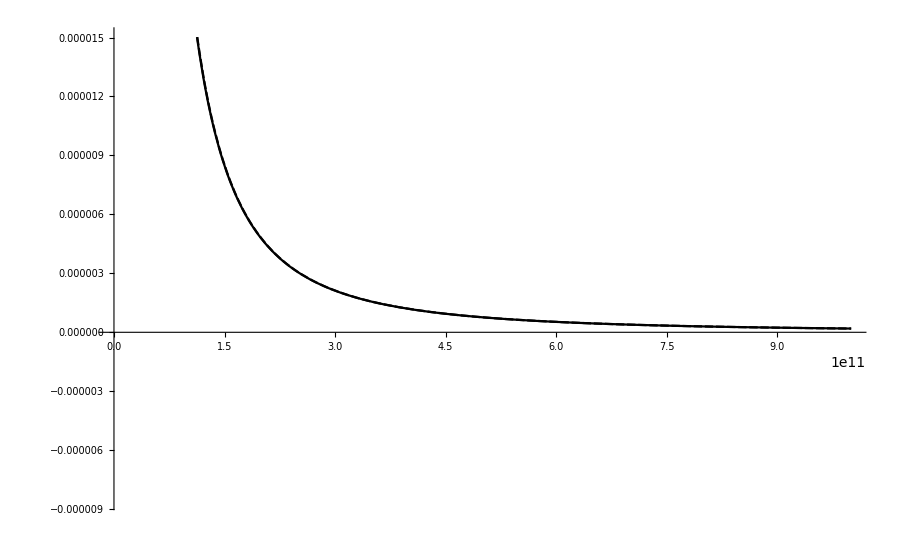

```mathematica
Plot[{getW[cpu,op,l,maxV, 0, 1], getW[cpu,op,l,maxV, 0, 4]},{cpu,10^5,10^12},PlotTheme->"Monochrome"]
```

```mathematica
flist =Table[{0.5*1024/5*40,1024 / 15 * 60,0,2.5 * 1024 / 10 * 10,4 * 1024 / 20 * 10}]
o1 = Table[{1024 / 15 * 10,  4 * 1024 / 20 * 6}]
o2 = Table[{1024 / 8 * 16, 1.5  * 1024 }]
f2list = Table[{1024 / 8 * 126, 1.5*1024/6*64, 2 * 1024 / 18 * 20, 3 * 1024 / 15 * 8, 4.5 * 1024 / 25 * 13}]
o = 2*10^8 + 7 * 10^8 + 9*10^8 + 5 * 10^8 + 9 * 10^8 + Total[flist + f2list] + 1

o = Total[o1 + o2] * 2 + 200+ 1

nNorm = {{0, 1, 1, 1, 0, 0, 0, 0, 1, 0}, {1, 0, 0, 1, 0, 0, 1, 0, 1, 0}, {1, 1, 0, 1, 0, 0, 0, 0, 0, 1}, {0, 1, 1, 0, 0, 1, 0, 1, 0, 1}, {0, 1, 0, 1, 0, 0, 1, 0, 0, 1}}

vRZY1 = {0.5 * 1024, 0, 1024, 0, 1.5 * 1024, 0, 2.5 * 1024, 0, 4 * 1024, 0}
vRZY2 = {0, 1024, 0, 1.5 * 1024, 0, 2 * 1024, 0, 3 * 1024, 0, 4.5 * 1024}
gVZY1 = {5, 0, 15, 0, 14, 0, 10, 0, 20, 0}
gVZY2 = {0, 8, 0, 6, 0, 18, 0, 15, 0, 25}
qFVZY1 = {1, 0, 2, 0, 3, 0, 2.5, 0, 2.5, 0}
qFVZY2 = {0, 0.1, 0, 0.05, 0, 0.06, 0, 0.13, 0, 0.12}
```

{4096.,4096,0,2560.,2048}

{2048/3,6144/5}

{2048,1536.}

{16128,16384.,20480/9,8192/5,2396.16}

3.20005×10^9

11191.9

{{0,1,1,1,0,0,0,0,1,0},{1,0,0,1,0,0,1,0,1,0},{1,1,0,1,0,0,0,0,0,1},{0,1,1,0,0,1,0,1,0,1},{0,1,0,1,0,0,1,0,0,1}}

```mathematica
oProc = o - Total[o1 + o2]
```

2.×10^8

```mathematica
p12 = Total[o1]/o
p13 = Total[o2] / o
p10 = Total[o1 + o2] / o
p11 = 1 - p10 - p12 - p13
```

0.17079

0.320231

0.49102

0.0179594

```mathematica
a = {9, 8, 7, 6, 5, 4, 3, 2, 1, 0}
b  = Table[a[[i]], {i, 1, 3}]
Total[b]
```

{9,8,7,6,5,4,3,2,1,0}

{9,8,7}